```mathematica
ClearAll["Global`*"]
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/channel_with_cylinder_flat_cn/solution_1/data.csv"];
t1=Table[{t1[[i,1]],Log[Abs[t1[[i,4]]]]/Log[10]},{i,2,Length[t1]}]
```

```mathematica
t2=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/channel_with_cylinder_flat_cn/solution_2/data.csv"];
t2=Table[{t2[[i,1]]/2,Log[Abs[t2[[i,4]]]]/Log[10]},{i,2,Length[t2]}]
```

```mathematica
t3=Import["/Users/michelecastellana/Documents/finite_elements/dynamics/channel_with_cylinder_flat_cn/solution/data.csv"];
t3=Table[{t3[[i,1]]/4,Log[Abs[t3[[i,4]]]]/Log[10]},{i,2,Length[t3]}]
```

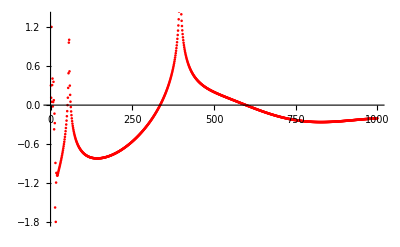

```mathematica
plot1=ListPlot[t1,PlotStyle->Red]
```

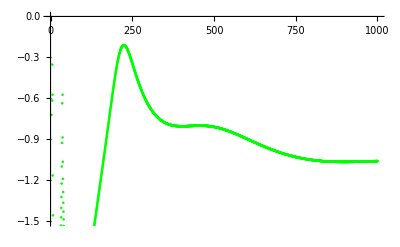

```mathematica
plot2=ListPlot[t2,PlotStyle->Green]
```

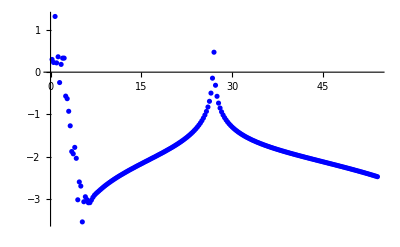

```mathematica
plot3=ListPlot[t3,PlotStyle->Blue]
```

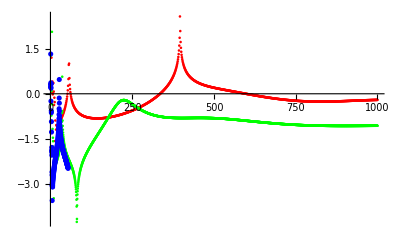

```mathematica
Show[plot1,plot2,plot3,PlotRange->Full]
```